2 PRACTICAL (N-Method R)

Question

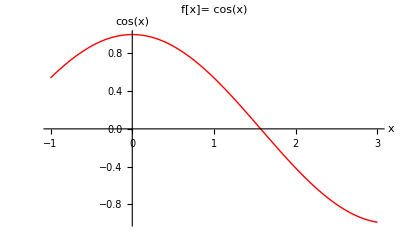

```mathematica
PRACTICAL 2 (N-R Method)

Question 1

f[x_] := Cos[x];
Plot[f[x],{x,-1,3}, PlotStyle->{Red,Thick},
AxesLabel->{x,f[x]}, PlotLabel->"f[x]="f[x]]
```

```mathematica
x0=1;
Nmax=20;
eps=10^(-6);
Print["f[x]=",f[x]];
Print["f[x]=",D[f[x],x]];
For[i=1,i≤Nmax,i++,x1=N[x0-(f[x]/.x->x0)/(D[f[x],x]/.x->x0)];
If[Abs[x1-x0]<eps,Return[x1],x0p=x0;x0=x1];
Print["In",i,"the Number of iteration the approximation to root is:",x1];
Print["Estimated error is :",Abs[x1-x0p]]];
Print["the final apporximation of root is:",x1];
Print["Estimated error is : ",Abs[x1-x0]]
```

f[x]=Cos[x]

f[x]=-Sin[x]

In1the Number of iteration the approximation to root is:1.64209

Estimated error is :0.642093

In2the Number of iteration the approximation to root is:1.57068

Estimated error is :0.0714173

In3the Number of iteration the approximation to root is:1.5708

Estimated error is :0.00012105

Return[1.5708]

the final apporximation of root is:1.5708

Estimated error is : 5.91305×10^-13

# ques 2

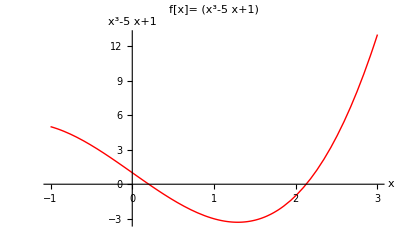

```mathematica
f[x_] = x^3-5*x+1 ;
Plot[f[x],{x,-1,3}, PlotStyle->{Red,Thick},
AxesLabel->{x,f[x]}, PlotLabel->"f[x]="f[x]]
```

```mathematica
x0=0.5;
Nmax=20;
eps=10^(-6);
Print["f[x]=",f[x]];
Print["f[x]=",D[f[x],x]];
For[i=1,i≤Nmax,i++,x1=N[x0-(f[x]/.x->x0)/(D[f[x],x]/.x->x0)];
If[Abs[x1-x0]<eps,Return[x1],x0p=x0;x0=x1];
Print["In",i,"the Number of iteration the approximation to root is:",x1];
Print["Estimated error is :",Abs[x1-x0p]]];
Print["the final apporximation of root is:",x1];
Print["Estimated error is : ",Abs[x1-x0]]
```

f[x]=1-5 x+x^3

f[x]=-5+3 x^2

In1the Number of iteration the approximation to root is:0.176471

Estimated error is :0.323529

In2the Number of iteration the approximation to root is:0.201568

Estimated error is :0.0250975

In3the Number of iteration the approximation to root is:0.20164

Estimated error is :0.0000716007

Return[0.20164]

the final apporximation of root is:0.20164

Estimated error is : 6.35602×10^-10

# ques3

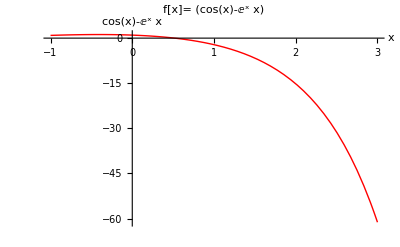

```mathematica
f[x_] = Cos[x]-x*Exp[x];
Plot[f[x],{x,-1,3}, PlotStyle->{Red,Thick},
AxesLabel->{x,f[x]}, PlotLabel->"f[x]="f[x]]
```

```mathematica
x0=1.5;
Nmax=20;
eps=10^(-6);
Print["f[x]=",f[x]];
Print["f[x]=",D[f[x],x]];
For[i=1,i≤Nmax,i++,x1=N[x0-(f[x]/.x->x0)/(D[f[x],x]/.x->x0)];
If[Abs[x1-x0]<eps,Return[x1],x0p=x0;x0=x1];
Print["In",i,"the Number of iteration the approximation to root is:",x1];
Print["Estimated error is :",Abs[x1-x0p]]];
Print["the final apporximation of root is:",x1];
Print["Estimated error is : ",Abs[x1-x0]]
```

f[x]=-ⅇ^x x+Cos[x]

f[x]=-ⅇ^x-ⅇ^x x-Sin[x]

In1the Number of iteration the approximation to root is:0.954848

Estimated error is :0.545152

In2the Number of iteration the approximation to root is:0.632019

Estimated error is :0.322829

In3the Number of iteration the approximation to root is:0.527616

Estimated error is :0.104403

In4the Number of iteration the approximation to root is:0.517838

Estimated error is :0.00977784

In5the Number of iteration the approximation to root is:0.517757

Estimated error is :0.0000806043

Return[0.517757]

the final apporximation of root is:0.517757

Estimated error is : 5.44033×10^-9